# Modelling menstrual cycle dynamics

## Plotting real data

Ticks→{{0.835484 (60.+1.19691 γ)},Automatic}

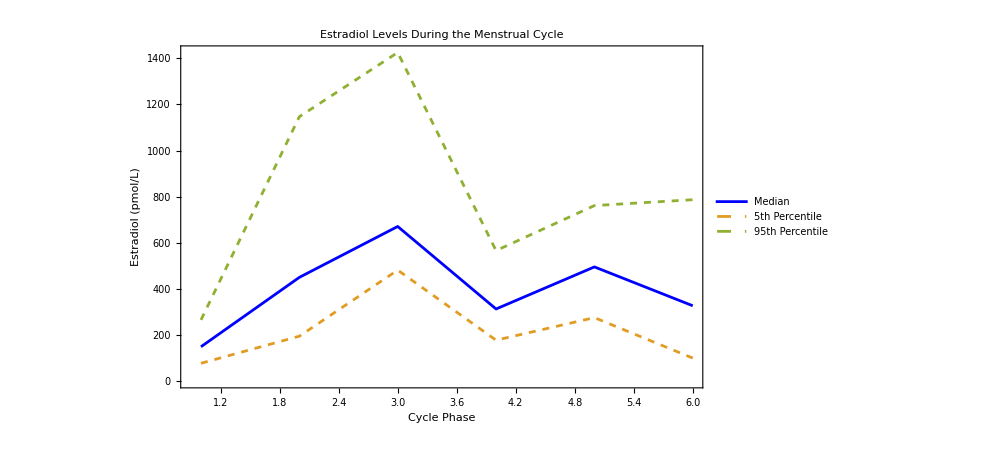

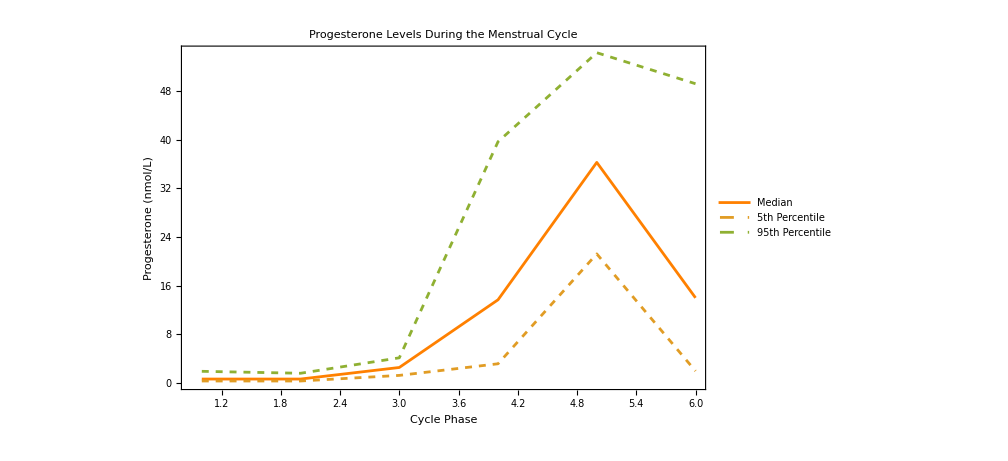

```mathematica
(*Data for the menstrual cycle phases*)phases={"Early Follicular","Late Follicular","LH Peak","Early Luteal","Mid-Luteal","Late Luteal"};

(*Estradiol data (median,5th,95th percentiles)*)
estradiolMedian={149.74,450.49,671.06,313.42,495.82,327.36};
estradiol5th={77.99,195.43,482.00,178.14,275.95,100.52};
estradiol95th={266.08,1146.91,1425.39,566.43,761.67,787.14};
Ticks->{{0.835484 (60.+1.19691 γ)},Automatic}
(*Progesterone data (median,5th,95th percentiles)*)
progesteroneMedian={0.64,0.64,2.54,13.67,36.25,13.99};
progesterone5th={0.32,0.32,1.24,3.15,21.21,1.96};
progesterone95th={1.91,1.59,4.13,39.65,54.28,49.18};

estradiolPlot=ListLinePlot[{estradiolMedian,estradiol5th,estradiol95th},PlotStyle->{Blue,Dashed,Dashed},PlotLegends->{"Median","5th Percentile","95th Percentile"},Frame->True,FrameLabel->{"Cycle Phase","Estradiol (pmol/L)"},LabelStyle->{Bold,12},PlotRange->All,PlotLabel->Style["Estradiol Levels During the Menstrual Cycle",Bold,14]];

(*Create progesterone plot*)
progesteronePlot=ListLinePlot[{progesteroneMedian,progesterone5th,progesterone95th},PlotStyle->{Orange,Dashed,Dashed},PlotLegends->{"Median","5th Percentile","95th Percentile"},Frame->True,FrameLabel->{"Cycle Phase","Progesterone (nmol/L)"},PlotRange->All,PlotLabel->Style["Progesterone Levels During the Menstrual Cycle",Bold,14]];

(*Display plots*)
estradiolPlot 
progesteronePlot
```

## Modelling estradiol and progesterone

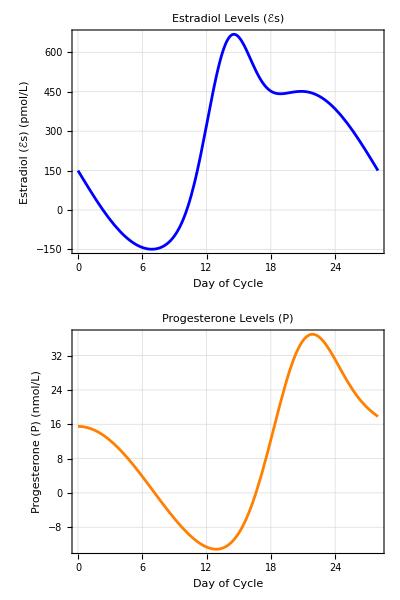

```mathematica
(*Define parameters for the estradiol model*)Es0=150; (*Baseline estradiol level in pmol/L*)
AEs=300; (*Amplitude of estradiol sinusoidal component*)
phiEs=14; (*Phase shift to align estradiol peak with ovulation*)
kEs=500; (*Scaling factor for estradiol LH peak*)
tLH=14; (*Day of LH peak*)
sigmaLH=2; (*Width of LH peak*)

(*Define estradiol function*)
Es[t_]:=Es0+AEs Sin[(2 Pi/28) (t-phiEs)]+kEs Exp[-((t-tLH)^2)/(2 sigmaLH^2)];

(*Define parameters for the progesterone model*)
P0=0.5; (*Baseline progesterone level in nmol/L*)
AP=15; (*Amplitude of progesterone sinusoidal component*)
phiP=21; (*Phase shift to align progesterone peak with mid-luteal phase*)
kP=35; (*Scaling factor for luteal phase peak*)
tLuteal=21; (*Day of mid-luteal peak*)
sigmaLuteal=3; (*Width of luteal peak*)

(*Define progesterone function*)
P[t_]:=P0+AP Sin[(2 Pi/28) (t-phiP)]+kP Exp[-((t-tLuteal)^2)/(2 sigmaLuteal^2)];

(*Plot estradiol and progesterone*)
estradiolPlot=Plot[Es[t],{t,0,28},PlotStyle->Blue,PlotLabel->Style["Estradiol Levels (ℰs)",Bold,14],Frame->True,FrameLabel->{"Day of Cycle","Estradiol (ℰs) (pmol/L)"},GridLines->Automatic,ImageSize->Large];

progesteronePlot=Plot[P[t],{t,0,28},PlotStyle->Orange,PlotLabel->Style["Progesterone Levels (P)",Bold,14],Frame->True,FrameLabel->{"Day of Cycle","Progesterone (P) (nmol/L)"},GridLines->Automatic,ImageSize->Large];

(*Combine the plots in a grid*)
Grid[{{estradiolPlot},{progesteronePlot}}]
```

## Comparing real data vs model

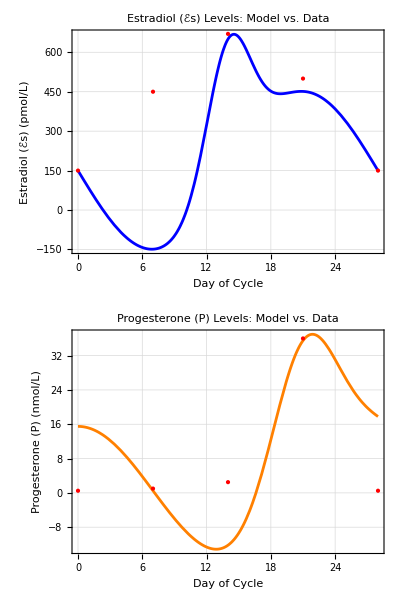

```mathematica
(*Real data for estradiol and progesterone*)realDataEs={{0,150},{7,450},{14,670},{21,500},{28,150}};
realDataP={{0,0.5},{7,1},{14,2.5},{21,36},{28,0.5}};

(*Model plots with real data overlaid*)
estradiolPlotWithData=Show[Plot[Es[t],{t,0,28},PlotStyle->Blue],ListPlot[realDataEs,PlotStyle->{Red,PointSize[Large]}],PlotLabel->Style["Estradiol (ℰs) Levels: Model vs. Data",Bold,14],Frame->True,FrameLabel->{"Day of Cycle","Estradiol (ℰs) (pmol/L)"},GridLines->Automatic,ImageSize->Large];

progesteronePlotWithData=Show[Plot[P[t],{t,0,28},PlotStyle->Orange],ListPlot[realDataP,PlotStyle->{Red,PointSize[Large]}],PlotLabel->Style["Progesterone (P) Levels: Model vs. Data",Bold,14],Frame->True,FrameLabel->{"Day of Cycle","Progesterone (P) (nmol/L)"},GridLines->Automatic,ImageSize->Large];

Grid[{{estradiolPlotWithData},{progesteronePlotWithData}}]
```

## Updating the estradiol and progesterone models

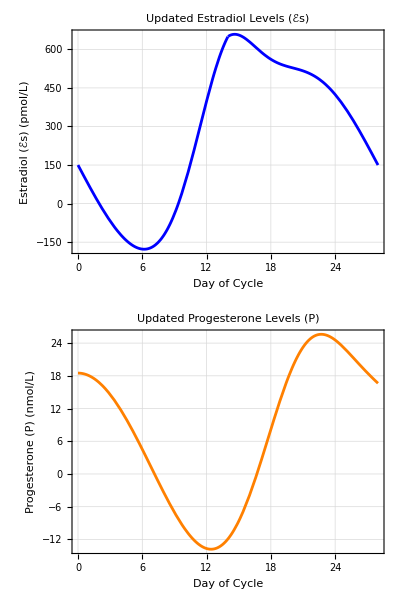

```mathematica
(*Updated parameters for the estradiol model*)Es0=150; (*Baseline estradiol level in pmol/L*)
AEs=350; (*Adjusted amplitude of estradiol sinusoidal component*)
phiEs=14; (*Phase shift to align estradiol peak with ovulation*)
kEs=500; (*Scaling factor for estradiol LH peak*)
tLH=14; (*Day of LH peak*)
sigmaLH=3; (*Increased width of LH peak*)
betaEs=0.1; (*Exponential decay factor for estradiol in luteal phase*)

(*Updated estradiol function*)
Es[t_]:=Es0+AEs Sin[(2 Pi/28) (t-phiEs)]+kEs Exp[-((t-tLH)^2)/(2 sigmaLH^2)] Exp[-betaEs Max[0,t-tLH]];

(*Updated parameters for the progesterone model*)
P0=0.5; (*Baseline progesterone level in nmol/L*)
AP=18; (*Slightly increased amplitude of progesterone sinusoidal component*)
phiP=21; (*Phase shift to align progesterone peak with mid-luteal phase*)
kP=30; (*Reduced scaling factor for luteal phase peak*)
tLuteal=21; (*Day of mid-luteal peak*)
sigmaLuteal=4; (*Increased width of luteal peak*)
gammaP=10; (*Scaling factor for post-peak decline*)
sigmaDecline=5; (*Width of post-peak decline*)

(*Updated progesterone function*)
P[t_]:=P0+AP Sin[(2 Pi/28) (t-phiP)]+kP Exp[-((t-tLuteal)^2)/(2 sigmaLuteal^2)]-gammaP Exp[-((t-(tLuteal+sigmaLuteal))^2)/(2 sigmaDecline^2)];

(*Plot updated estradiol and progesterone functions*)
estradiolPlot=Plot[Es[t],{t,0,28},PlotStyle->Blue,PlotLabel->Style["Updated Estradiol Levels (ℰs)",Bold,14],Frame->True,FrameLabel->{"Day of Cycle","Estradiol (ℰs) (pmol/L)"},GridLines->Automatic,ImageSize->Large];

progesteronePlot=Plot[P[t],{t,0,28},PlotStyle->Orange,PlotLabel->Style["Updated Progesterone Levels (P)",Bold,14],Frame->True,FrameLabel->{"Day of Cycle","Progesterone (P) (nmol/L)"},GridLines->Automatic,ImageSize->Large];

(*Combine the updated plots in a grid*)
Grid[{{estradiolPlot},{progesteronePlot}}]
```

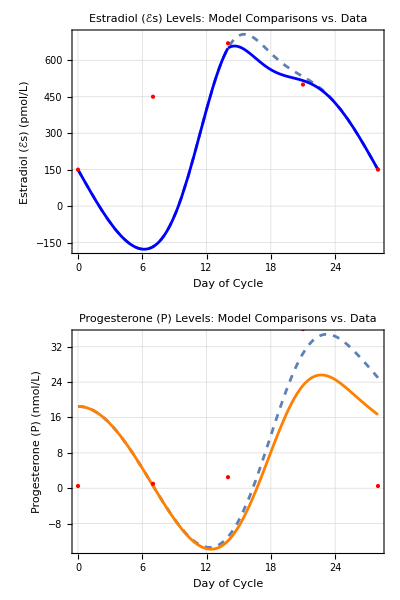

```mathematica
(*Real data for estradiol and progesterone*)realDataEs={{0,150},{7,450},{14,670},{21,500},{28,150}};
realDataP={{0,0.5},{7,1},{14,2.5},{21,36},{28,0.5}};

(*Original estradiol function*)
originalEs[t_]:=Es0+AEs Sin[(2 Pi/28) (t-phiEs)]+kEs Exp[-((t-tLH)^2)/(2 sigmaLH^2)];

(*Updated estradiol function*)
updatedEs[t_]:=Es0+AEs Sin[(2 Pi/28) (t-phiEs)]+kEs Exp[-((t-tLH)^2)/(2 sigmaLH^2)] Exp[-betaEs Max[0,t-tLH]];

(*Original progesterone function*)
originalP[t_]:=P0+AP Sin[(2 Pi/28) (t-phiP)]+kP Exp[-((t-tLuteal)^2)/(2 sigmaLuteal^2)];

(*Updated progesterone function*)
updatedP[t_]:=P0+AP Sin[(2 Pi/28) (t-phiP)]+kP Exp[-((t-tLuteal)^2)/(2 sigmaLuteal^2)]-gammaP Exp[-((t-(tLuteal+sigmaLuteal))^2)/(2 sigmaDecline^2)];

(*Compare estradiol models and real data*)
estradiolComparisonPlot=Show[Plot[{originalEs[t],updatedEs[t]},{t,0,28},PlotStyle->{Dashed,Blue}],ListPlot[realDataEs,PlotStyle->{Red,PointSize[Large]}],PlotLegends->Placed[{"Original Model","Updated Model","Real Data"},Above],PlotLabel->Style["Estradiol (ℰs) Levels: Model Comparisons vs. Data",Bold,14],Frame->True,FrameLabel->{"Day of Cycle","Estradiol (ℰs) (pmol/L)"},GridLines->Automatic,ImageSize->Large];

(*Compare progesterone models and real data*)
progesteroneComparisonPlot=Show[Plot[{originalP[t],updatedP[t]},{t,0,28},PlotStyle->{Dashed,Orange}],ListPlot[realDataP,PlotStyle->{Red,PointSize[Large]}],PlotLegends->Placed[{"Original Model","Updated Model","Real Data"},Above],PlotLabel->Style["Progesterone (P) Levels: Model Comparisons vs. Data",Bold,14],Frame->True,FrameLabel->{"Day of Cycle","Progesterone (P) (nmol/L)"},GridLines->Automatic,ImageSize->Large];

(*Display comparison plots in a grid*)
Grid[{{estradiolComparisonPlot},{progesteroneComparisonPlot}}]
```

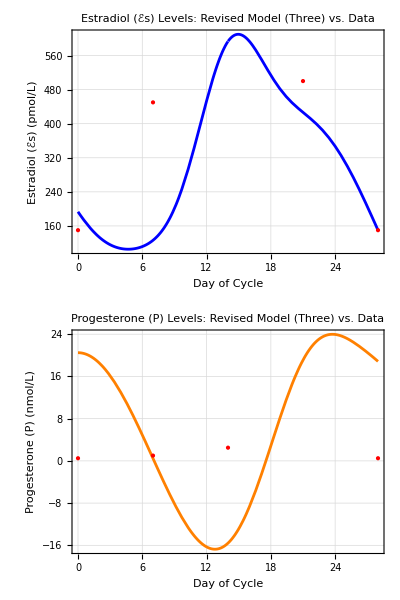

```mathematica
(*Modified estradiol parameters for smoother rise*)Es0Three=150; (*Baseline estradiol level in pmol/L*)
AEsThree=250; (*Adjusted amplitude for smoother sinusoidal rise*)
phiEsThree=14; (*Phase shift remains the same*)
kEsThree=400; (*Reduced scaling factor for main Gaussian peak*)
tLHThree=14; (*Day of LH peak*)
sigmaLHThree=3; (*Width of LH peak remains broader*)
kSmoothThree=200; (*New scaling factor for secondary Gaussian*)
tSmoothThree=7; (*Center of secondary Gaussian for late follicular rise*)
sigmaSmoothThree=4; (*Width of secondary Gaussian*)
betaEsThree=0.05; (*Exponential decay remains the same*)

(*Modified estradiol function for smoother rise*)
EsThree[t_]:=Es0Three+AEsThree Sin[(2 Pi/28) (t-phiEsThree)]+kEsThree Exp[-((t-tLHThree)^2)/(2 sigmaLHThree^2)]+kSmoothThree Exp[-((t-tSmoothThree)^2)/(2 sigmaSmoothThree^2)] Exp[-betaEsThree Max[0,t-tLHThree]];

(*Adjusted progesterone parameters*)
P0Three=0.5; (*Baseline progesterone level in nmol/L*)
APThree=20; (*Increased amplitude of progesterone sinusoidal component*)
phiPThree=21; (*Phase shift to align progesterone peak with mid-luteal phase*)
kPThree=25; (*Reduced scaling factor for luteal phase peak*)
tLutealThree=21; (*Day of mid-luteal peak*)
sigmaLutealThree=4; (*Width of luteal peak remains broader*)
gammaPThree=8; (*Reduced scaling factor for post-peak decline*)
sigmaDeclineThree=6; (*Broadened width for post-peak decline*)

(*Adjusted progesterone function*)
PThree[t_]:=P0Three+APThree Sin[(2 Pi/28) (t-phiPThree)]+kPThree Exp[-((t-tLutealThree)^2)/(2 sigmaLutealThree^2)]-gammaPThree Exp[-((t-(tLutealThree+sigmaLutealThree))^2)/(2 sigmaDeclineThree^2)];

(*Compare new estradiol model with real data*)
estradiolPlotWithDataThree=Show[Plot[EsThree[t],{t,0,28},PlotStyle->Blue],ListPlot[realDataEs,PlotStyle->{Red,PointSize[Large]}],PlotLabel->Style["Estradiol (ℰs) Levels: Revised Model (Three) vs. Data",Bold,14],Frame->True,FrameLabel->{"Day of Cycle","Estradiol (ℰs) (pmol/L)"},GridLines->Automatic,ImageSize->Large];

(*Compare new progesterone model with real data*)
progesteronePlotWithDataThree=Show[Plot[PThree[t],{t,0,28},PlotStyle->Orange],ListPlot[realDataP,PlotStyle->{Red,PointSize[Large]}],PlotLabel->Style["Progesterone (P) Levels: Revised Model (Three) vs. Data",Bold,14],Frame->True,FrameLabel->{"Day of Cycle","Progesterone (P) (nmol/L)"},GridLines->Automatic,ImageSize->Large];

(*Display revised plots in a grid*)
Grid[{{estradiolPlotWithDataThree},{progesteronePlotWithDataThree}}]
```

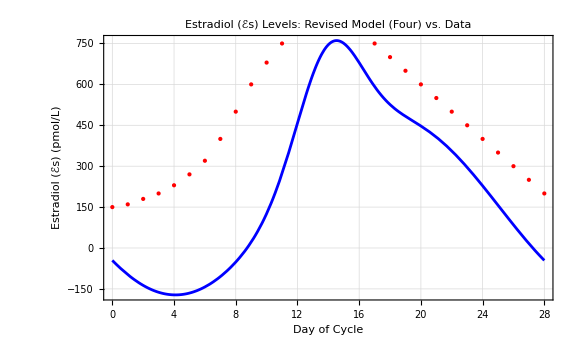

```mathematica
(*Detailed real data points for estradiol*)realDataEsDetailed={{0,150},{1,160},{2,180},{3,200},{4,230},{5,270},{6,320},{7,400},{8,500},{9,600},{10,680},{11,750},{12,800},{13,850},{14,900},{15,850},{16,800},{17,750},{18,700},{19,650},{20,600},{21,550},{22,500},{23,450},{24,400},{25,350},{26,300},{27,250},{28,200}};

(*Adjusted estradiol parameters for smoother rise*)
Es0Four=150; (*Baseline estradiol level in pmol/L*)
AEs1Four=100; (*Amplitude of first sinusoidal component*)
AEs2Four=250; (*Amplitude of second sinusoidal component*)
phiEs1Four=14; (*Phase shift of first sinusoidal component*)
phiEs2Four=10; (*Phase shift of second sinusoidal component*)
kEsFour=400; (*Scaling factor for main Gaussian peak*)
tLHFour=14; (*Day of LH peak*)
sigmaLHFour=2; (*Width of LH peak remains narrower*)

(*Adjusted estradiol function with dual sinusoidal components*)
EsFour[t_]:=Es0Four+AEs1Four Sin[(2 Pi/28) (t-phiEs1Four)]+AEs2Four Sin[(2 Pi/28) (t-phiEs2Four)]+kEsFour Exp[-((t-tLHFour)^2)/(2 sigmaLHFour^2)];

(*Plot updated estradiol function with detailed real data*)
estradiolPlotWithDetailedDataFour=Show[Plot[EsFour[t],{t,0,28},PlotStyle->Blue],ListPlot[realDataEsDetailed,PlotStyle->{Red,PointSize[Large]}],PlotLabel->Style["Estradiol (ℰs) Levels: Revised Model (Four) vs. Data",Bold,14],Frame->True,FrameLabel->{"Day of Cycle","Estradiol (ℰs) (pmol/L)"},GridLines->Automatic,ImageSize->Large];

(*Display the plot*)
estradiolPlotWithDetailedDataFour
```

```mathematica
(*Adjusted progesterone parameters for Four iteration*)P0Four=0.5; (*Baseline progesterone level in nmol/L*)
APFour=20; (*Increased amplitude of progesterone sinusoidal component*)
phiPFour=21; (*Phase shift of sinusoidal component*)
kPFour=25; (*Reduced scaling factor for luteal phase peak*)
tLutealFour=21; (*Day of mid-luteal peak*)
sigmaLutealFour=4; (*Width of luteal peak*)
gammaPFour=8; (*Reduced scaling factor for post-peak decline*)
sigmaDeclineFour=6; (*Broadened width for post-peak decline*)

(*Adjusted progesterone function with smoother transitions*)
PFour[t_]:=P0Four+APFour Sin[(2 Pi/28) (t-phiPFour)]+kPFour Exp[-((t-tLutealFour)^2)/(2 sigmaLutealFour^2)]-gammaPFour Exp[-((t-(tLutealFour+sigmaLutealFour))^2)/(2 sigmaDeclineFour^2)];

(*Detailed real data points for progesterone*)
realDataPFour={{0,0.5},{1,0.6},{2,0.7},{3,0.8},{4,1},{5,1.2},{6,1.5},{7,2},{8,3},{9,5},{10,8},{11,12},{12,18},{13,25},{14,30},{15,32},{16,34},{17,35},{18,36},{19,36},{20,35},{21,34},{22,30},{23,25},{24,20},{25,15},{26,10},{27,5},{28,0.5}};

(*Plot updated progesterone function with real data*)
progesteronePlotWithDetailedDataFour=Show[Plot[PFour[t],{t,0,28},PlotStyle->Orange],ListPlot[realDataPFour,PlotStyle->{Red,PointSize[Large]}],PlotLabel->Style["Progesterone (P) Levels: Revised Model (Four) vs. Data",Bold,14],Frame->True,FrameLabel->{"Day of Cycle","Progesterone (P) (nmol/L)"},GridLines->Automatic,ImageSize->Large];
```

```mathematica
progesteronePlotWithDetailedDataFour
```

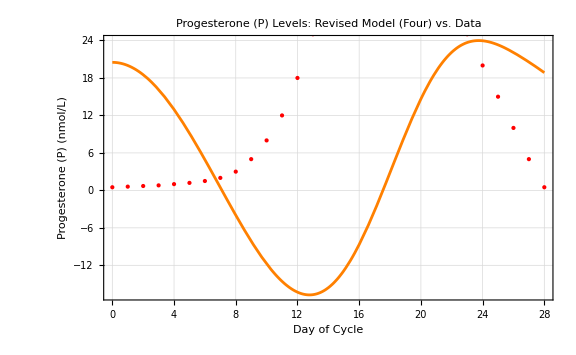

```mathematica
(*Original,Three,and Four estradiol functions*)EsOriginal[t_]:=Es0+AEs Sin[(2 Pi/28) (t-phiEs)]+kEs Exp[-((t-tLH)^2)/(2 sigmaLH^2)];
EsThree[t_]:=Es0Three+AEsThree Sin[(2 Pi/28) (t-phiEsThree)]+kEsThree Exp[-((t-tLHThree)^2)/(2 sigmaLHThree^2)];
(*Four already defined as EsFour[t]*)

(*Plot all models and real data together for estradiol*)
estradiolComparisonAll=Show[Plot[{EsOriginal[t],EsThree[t],EsFour[t]},{t,0,28},PlotStyle->{Dashed,Dotted,Blue}],ListPlot[realDataEsDetailed,PlotStyle->{Red,PointSize[Large]}],PlotLegends->Placed[{"Original","Three","Four","Real Data"},Above],PlotLabel->Style["Estradiol (ℰs) Levels: All Models vs. Data",Bold,14],Frame->True,FrameLabel->{"Day of Cycle","Estradiol (ℰs) (pmol/L)"},GridLines->Automatic,ImageSize->Large];
```

```mathematica
estradiolComparisonAll
```

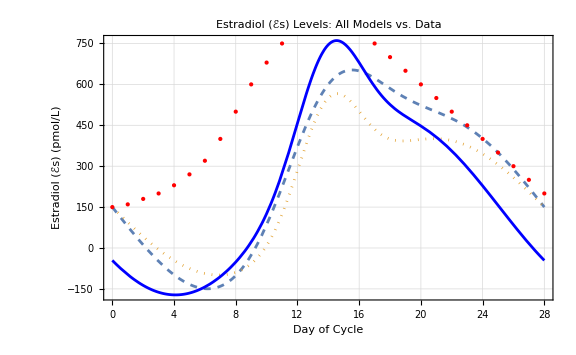
```mathematica
-Graphics-
(*Original,Three,and Four progesterone functions*)POriginal[t_]:=P0+AP Sin[(2 Pi/28) (t-phiP)]+kP Exp[-((t-tLuteal)^2)/(2 sigmaLuteal^2)];
PThree[t_]:=P0Three+APThree Sin[(2 Pi/28) (t-phiPThree)]+kPThree Exp[-((t-tLutealThree)^2)/(2 sigmaLutealThree^2)]-gammaPThree Exp[-((t-(tLutealThree+sigmaLutealThree))^2)/(2 sigmaDeclineThree^2)];
(*Four already defined as PFour[t]*)

(*Plot all models and real data together for progesterone*)
progesteroneComparisonAll=Show[Plot[{POriginal[t],PThree[t],PFour[t]},{t,0,28},PlotStyle->{Dashed,Dotted,Orange}],ListPlot[realDataPFour,PlotStyle->{Red,PointSize[Large]}],PlotLegends->Placed[{"Original","Three","Four","Real Data"},Above],PlotLabel->Style["Progesterone (P) Levels: All Models vs. Data",Bold,14],Frame->True,FrameLabel->{"Day of Cycle","Progesterone (P) (nmol/L)"},GridLines->Automatic,ImageSize->Large];

progesteroneComparisonAll
```

-Graphics-

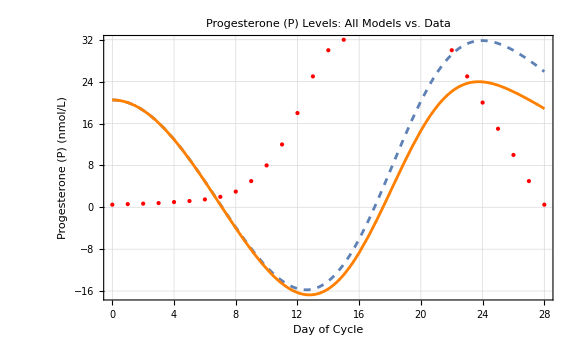
```mathematica
-Graphics-
(*Plot real data for estradiol*)realDataEsPlot=ListPlot[realDataEsDetailed,PlotStyle->{Red,PointSize[Large]},PlotLabel->Style["Estradiol (ℰs) Real Data",Bold,14],Frame->True,FrameLabel->{"Day of Cycle","Estradiol (ℰs) (pmol/L)"},GridLines->Automatic,ImageSize->Large];

realDataEsPlot
```

-Graphics-

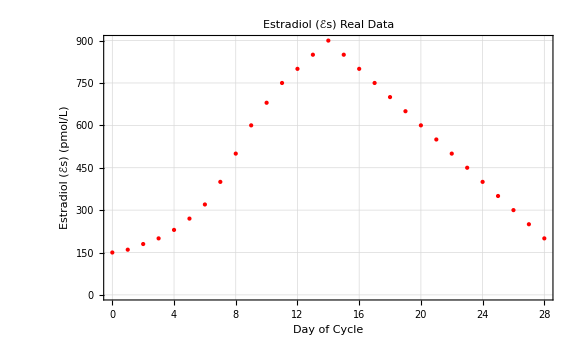

-Graphics-

-Graphics-

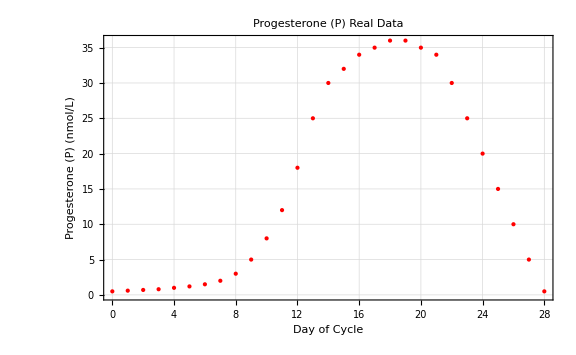

```mathematica
-Graphics-

realDataEsPlot

(*Plot real data for progesterone*)realDataPPlot=ListPlot[realDataPFour,PlotStyle->{Red,PointSize[Large]},PlotLabel->Style["Progesterone (P) Real Data",Bold,14],Frame->True,FrameLabel->{"Day of Cycle","Progesterone (P) (nmol/L)"},GridLines->Automatic,ImageSize->Large];

realDataPPlot
```

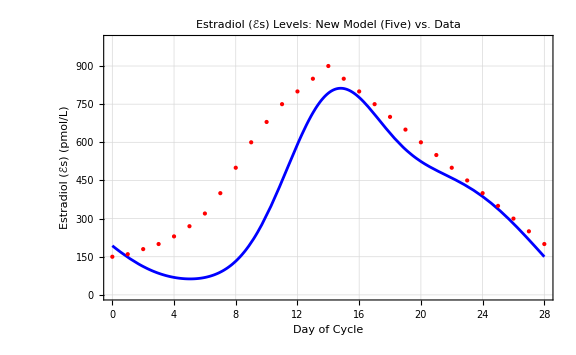

```mathematica
(*New estradiol parameters*)Es0Five=150; (*Baseline estradiol level in pmol/L*)
AEs1Five=300; (*Amplitude for the sinusoidal component*)
phiEs1Five=14; (*Phase shift to align peak*)
kEs1Five=600; (*Scaling factor for ovulatory Gaussian*)
tLHFive=14; (*Day of LH peak*)
sigmaLHFive=3; (*Width of LH peak Gaussian*)
kEs2Five=200; (*Smaller Gaussian for pre-ovulatory rise*)
tSmoothFive=7; (*Center of pre-ovulatory rise*)
sigmaSmoothFive=4; (*Width of pre-ovulatory Gaussian*)

(*New estradiol function*)
EsFive[t_]:=Es0Five+AEs1Five Sin[(2 Pi/28) (t-phiEs1Five)]+kEs1Five Exp[-((t-tLHFive)^2)/(2 sigmaLHFive^2)]+kEs2Five Exp[-((t-tSmoothFive)^2)/(2 sigmaSmoothFive^2)];

(*Plot new estradiol model with real data*)
estradiolPlotWithDataFive=Show[Plot[EsFive[t],{t,0,28},PlotStyle->Blue,PlotRange->{0,1000},AxesOrigin->{0,0}],ListPlot[realDataEsDetailed,PlotStyle->{Red,PointSize[Large]}],PlotLabel->Style["Estradiol (ℰs) Levels: New Model (Five) vs. Data",Bold,14],Frame->True,FrameLabel->{"Day of Cycle","Estradiol (ℰs) (pmol/L)"},GridLines->Automatic,ImageSize->Large];

estradiolPlotWithDataFive
```

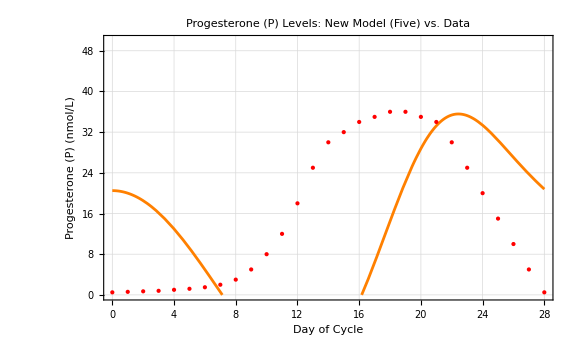

```mathematica
(*New progesterone parameters*)P0Five=0.5; (*Baseline progesterone level in nmol/L*)
APFive=20; (*Sinusoidal amplitude*)
phiPFive=21; (*Phase shift to align peak*)
kPFive=40; (*Scaling factor for mid-luteal Gaussian*)
tLutealFive=21; (*Day of mid-luteal peak*)
sigmaLutealFive=4; (*Width of mid-luteal Gaussian*)
gammaPFive=10; (*Scaling factor for post-peak Gaussian decline*)
sigmaDeclineFive=5; (*Width of post-peak decline*)

(*New progesterone function*)
PFive[t_]:=P0Five+APFive Sin[(2 Pi/28) (t-phiPFive)]+kPFive Exp[-((t-tLutealFive)^2)/(2 sigmaLutealFive^2)]-gammaPFive Exp[-((t-(tLutealFive+sigmaLutealFive))^2)/(2 sigmaDeclineFive^2)];

(*Plot new progesterone model with real data*)
progesteronePlotWithDataFive=Show[Plot[PFive[t],{t,0,28},PlotStyle->Orange,PlotRange->{0,50},AxesOrigin->{0,0}],ListPlot[realDataPFour,PlotStyle->{Red,PointSize[Large]}],PlotLabel->Style["Progesterone (P) Levels: New Model (Five) vs. Data",Bold,14],Frame->True,FrameLabel->{"Day of Cycle","Progesterone (P) (nmol/L)"},GridLines->Automatic,ImageSize->Large];

progesteronePlotWithDataFive
```

```mathematica
(*Define all estradiol models*)(*Original model*)EsOriginal[t_]:=Es0+AEs Sin[(2 Pi/28) (t-phiEs)]+kEs Exp[-((t-tLH)^2)/(2 sigmaLH^2)];

(*Three iteration*)
EsThree[t_]:=Es0Three+AEsThree Sin[(2 Pi/28) (t-phiEsThree)]+kEsThree Exp[-((t-tLHThree)^2)/(2 sigmaLHThree^2)];

(*Four iteration*)
EsFour[t_]:=Es0Four+AEs1Four Sin[(2 Pi/28) (t-phiEs1Four)]+kEsFour Exp[-((t-tLHFour)^2)/(2 sigmaLHFour^2)]+kEs2Four Exp[-((t-tSmoothFour)^2)/(2 sigmaSmoothFour^2)];

(*Five iteration*)
EsFive[t_]:=Es0Five+AEs1Five Sin[(2 Pi/28) (t-phiEs1Five)]+kEs1Five Exp[-((t-tLHFive)^2)/(2 sigmaLHFive^2)]+kEs2Five Exp[-((t-tSmoothFive)^2)/(2 sigmaSmoothFive^2)];

(*Plot all estradiol models with real data*)
estradiolComparisonAll=Show[Plot[{EsOriginal[t],EsThree[t],EsFour[t],EsFive[t]},{t,0,28},PlotStyle->{Dashed,Dotted,Blue,Green},PlotRange->{0,1000},AxesOrigin->{0,0}],ListPlot[realDataEsDetailed,PlotStyle->{Red,PointSize[Large]}],PlotLegends->Placed[{"Original","Three","Four","Five","Real Data"},Above],PlotLabel->Style["Estradiol (ℰs) Levels: All Models vs. Real Data",Bold,14],Frame->True,FrameLabel->{"Day of Cycle","Estradiol (ℰs) (pmol/L)"},GridLines->Automatic,ImageSize->Large];

estradiolComparisonAll
```

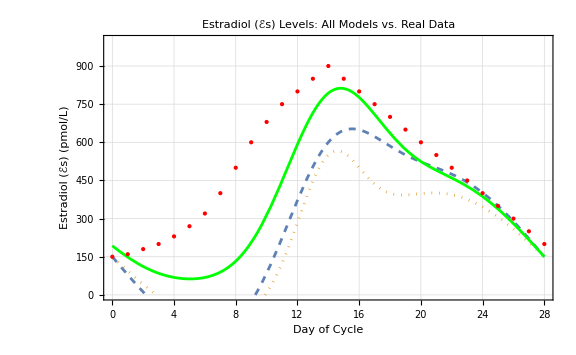

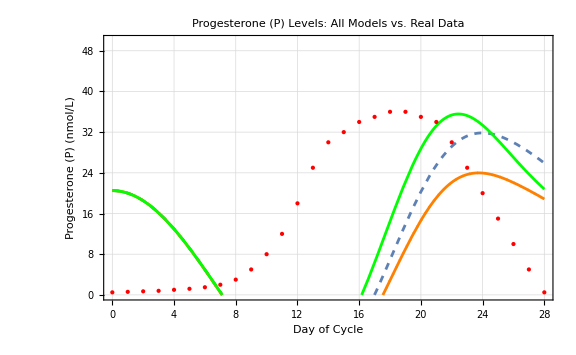

```mathematica
(*Define all progesterone models*)(*Original model*)POriginal[t_]:=P0+AP Sin[(2 Pi/28) (t-phiP)]+kP Exp[-((t-tLuteal)^2)/(2 sigmaLuteal^2)];

(*Three iteration*)
PThree[t_]:=P0Three+APThree Sin[(2 Pi/28) (t-phiPThree)]+kPThree Exp[-((t-tLutealThree)^2)/(2 sigmaLutealThree^2)]-gammaPThree Exp[-((t-(tLutealThree+sigmaLutealThree))^2)/(2 sigmaDeclineThree^2)];

(*Four iteration*)
PFour[t_]:=P0Four+APFour Sin[(2 Pi/28) (t-phiPFour)]+kPFour Exp[-((t-tLutealFour)^2)/(2 sigmaLutealFour^2)]-gammaPFour Exp[-((t-(tLutealFour+sigmaLutealFour))^2)/(2 sigmaDeclineFour^2)];

(*Five iteration*)
PFive[t_]:=P0Five+APFive Sin[(2 Pi/28) (t-phiPFive)]+kPFive Exp[-((t-tLutealFive)^2)/(2 sigmaLutealFive^2)]-gammaPFive Exp[-((t-(tLutealFive+sigmaLutealFive))^2)/(2 sigmaDeclineFive^2)];

(*Plot all progesterone models with real data*)
progesteroneComparisonAll=Show[Plot[{POriginal[t],PThree[t],PFour[t],PFive[t]},{t,0,28},PlotStyle->{Dashed,Dotted,Orange,Green},PlotRange->{0,50},AxesOrigin->{0,0}],ListPlot[realDataPFour,PlotStyle->{Red,PointSize[Large]}],PlotLegends->Placed[{"Original","Three","Four","Five","Real Data"},Above],PlotLabel->Style["Progesterone (P) Levels: All Models vs. Real Data",Bold,14],Frame->True,FrameLabel->{"Day of Cycle","Progesterone (P) (nmol/L)"},GridLines->Automatic,ImageSize->Large];

progesteroneComparisonAll
```

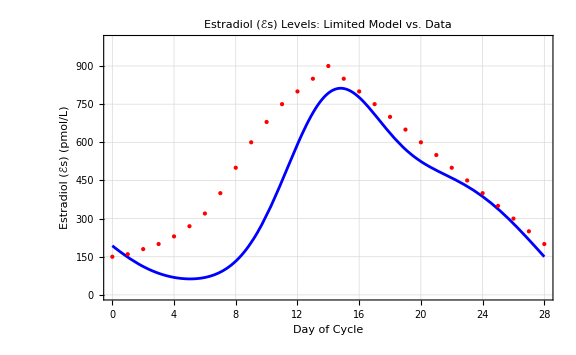

```mathematica
(*Add lower limit for estradiol*)estradiolLowerLimit=50;

(*Modified estradiol function with lower limit*)
EsFive[t_]:=Max[estradiolLowerLimit,Es0Five+AEs1Five Sin[(2 Pi/28) (t-phiEs1Five)]+kEs1Five Exp[-((t-tLHFive)^2)/(2 sigmaLHFive^2)]+kEs2Five Exp[-((t-tSmoothFive)^2)/(2 sigmaSmoothFive^2)]];

(*Add lower limit for progesterone*)progesteroneLowerLimit=0.5;

(*Modified progesterone function with lower limit*)
PFive[t_]:=Max[progesteroneLowerLimit,P0Five+APFive Sin[(2 Pi/28) (t-phiPFive)]+kPFive Exp[-((t-tLutealFive)^2)/(2 sigmaLutealFive^2)]-gammaPFive Exp[-((t-(tLutealFive+sigmaLutealFive))^2)/(2 sigmaDeclineFive^2)]];

(*Plot new estradiol model with limits and real data*)estradiolPlotWithLimits=Show[Plot[EsFive[t],{t,0,28},PlotStyle->Blue,PlotRange->{0,1000},AxesOrigin->{0,0}],ListPlot[realDataEsDetailed,PlotStyle->{Red,PointSize[Large]}],PlotLabel->Style["Estradiol (ℰs) Levels: Limited Model vs. Data",Bold,14],Frame->True,FrameLabel->{"Day of Cycle","Estradiol (ℰs) (pmol/L)"},GridLines->Automatic,ImageSize->Large];

estradiolPlotWithLimits
(*Plot new progesterone model with limits and real data*)progesteronePlotWithLimits=Show[Plot[PFive[t],{t,0,28},PlotStyle->Orange,PlotRange->{0,50},AxesOrigin->{0,0}],ListPlot[realDataPFour,PlotStyle->{Red,PointSize[Large]}],PlotLabel->Style["Progesterone (P) Levels: Limited Model vs. Data",Bold,14],Frame->True,FrameLabel->{"Day of Cycle","Progesterone (P) (nmol/L)"},GridLines->Automatic,ImageSize->Large];

progesteronePlotWithLimits
```

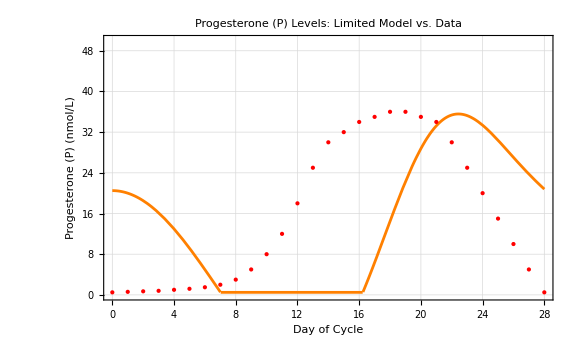

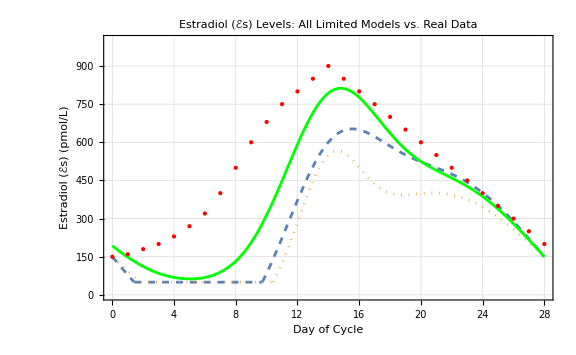

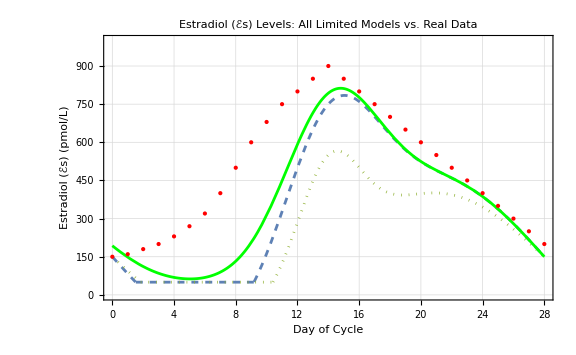

```mathematica
(*Lower limit for estradiol*)estradiolLowerLimit=50;

(*Original model with lower limit*)
EsOriginalLimited[t_]:=Max[estradiolLowerLimit,Es0+AEs Sin[(2 Pi/28) (t-phiEs)]+kEs Exp[-((t-tLH)^2)/(2 sigmaLH^2)]];

(*Updated/Second iteration with lower limit*)
EsUpdatedLimited[t_]:=Max[estradiolLowerLimit,Es0Updated+AEsUpdated Sin[(2 Pi/28) (t-phiEsUpdated)]+kEsUpdated Exp[-((t-tLHUpdated)^2)/(2 sigmaLHUpdated^2)]];

(*Three iteration with lower limit*)
EsThreeLimited[t_]:=Max[estradiolLowerLimit,Es0Three+AEsThree Sin[(2 Pi/28) (t-phiEsThree)]+kEsThree Exp[-((t-tLHThree)^2)/(2 sigmaLHThree^2)]];

(*Four iteration with lower limit*)
EsFourLimited[t_]:=Max[estradiolLowerLimit,Es0Four+AEs1Four Sin[(2 Pi/28) (t-phiEs1Four)]+kEsFour Exp[-((t-tLHFour)^2)/(2 sigmaLHFour^2)]+kEs2Four Exp[-((t-tSmoothFour)^2)/(2 sigmaSmoothFour^2)]];

(*Five iteration with lower limit*)
EsFiveLimited[t_]:=Max[estradiolLowerLimit,Es0Five+AEs1Five Sin[(2 Pi/28) (t-phiEs1Five)]+kEs1Five Exp[-((t-tLHFive)^2)/(2 sigmaLHFive^2)]+kEs2Five Exp[-((t-tSmoothFive)^2)/(2 sigmaSmoothFive^2)]];

(*Plot all limited estradiol models with real data*)
estradiolComparisonLimitedAll=Show[Plot[{EsOriginalLimited[t],EsUpdatedLimited[t],EsThreeLimited[t],EsFourLimited[t],EsFiveLimited[t]},{t,0,28},PlotStyle->{Dashed,DotDashed,Dotted,Blue,Green},PlotRange->{0,1000},AxesOrigin->{0,0}],ListPlot[realDataEsDetailed,PlotStyle->{Red,PointSize[Large]}],PlotLegends->Placed[{"Original Limited","Updated Limited","Three Limited","Four Limited","Five Limited","Real Data"},Above],PlotLabel->Style["Estradiol (ℰs) Levels: All Limited Models vs. Real Data",Bold,14],Frame->True,FrameLabel->{"Day of Cycle","Estradiol (ℰs) (pmol/L)"},GridLines->Automatic,ImageSize->Large];

estradiolComparisonLimitedAll
```

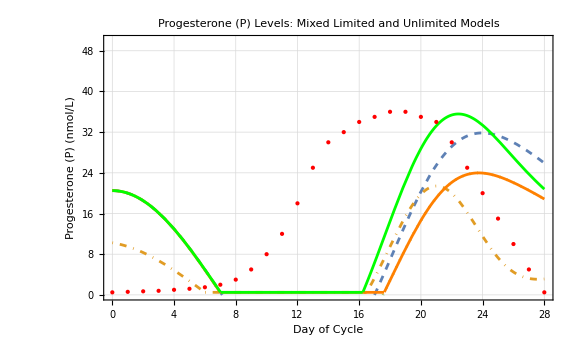

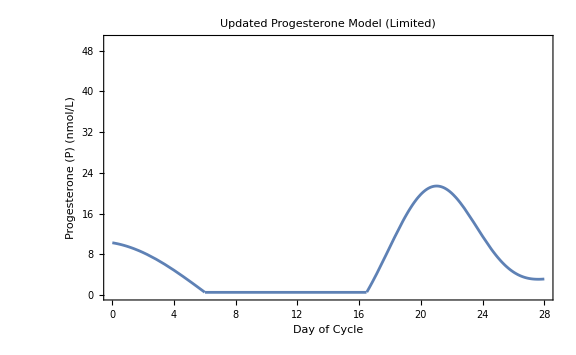

```mathematica
(*Lower limit for progesterone*)progesteroneLowerLimit=0.5;

(*Original model without lower limit*)
POriginal[t_]:=P0+AP Sin[(2 Pi/28) (t-phiP)]+kP Exp[-((t-tLuteal)^2)/(2 sigmaLuteal^2)];

(*Updated/Second iteration with lower limit*)
PUpdatedLimited[t_]:=Max[progesteroneLowerLimit,P0Updated+APUpdated Sin[(2 Pi/28) (t-phiPUpdated)]+kPUpdated Exp[-((t-tLutealUpdated)^2)/(2 sigmaLutealUpdated^2)]-gammaPUpdated Exp[-((t-(tLutealUpdated+sigmaLutealUpdated))^2)/(2 sigmaDeclineUpdated^2)]];

(*Three iteration without lower limit*)
PThree[t_]:=P0Three+APThree Sin[(2 Pi/28) (t-phiPThree)]+kPThree Exp[-((t-tLutealThree)^2)/(2 sigmaLutealThree^2)]-gammaPThree Exp[-((t-(tLutealThree+sigmaLutealThree))^2)/(2 sigmaDeclineThree^2)];

(*Four iteration with lower limit*)
PFourLimited[t_]:=Max[progesteroneLowerLimit,P0Four+APFour Sin[(2 Pi/28) (t-phiPFour)]+kPFour Exp[-((t-tLutealFour)^2)/(2 sigmaLutealFour^2)]-gammaPFour Exp[-((t-(tLutealFour+sigmaLutealFour))^2)/(2 sigmaDeclineFour^2)]];

(*Five iteration with lower limit*)
PFiveLimited[t_]:=Max[progesteroneLowerLimit,P0Five+APFive Sin[(2 Pi/28) (t-phiPFive)]+kPFive Exp[-((t-tLutealFive)^2)/(2 sigmaLutealFive^2)]-gammaPFive Exp[-((t-(tLutealFive+sigmaLutealFive))^2)/(2 sigmaDeclineFive^2)]];

(*Plot all progesterone models*)
progesteroneComparison=Show[Plot[{POriginal[t],PUpdatedLimited[t],PThree[t],PFourLimited[t],PFiveLimited[t]},{t,0,28},PlotStyle->{Dashed,DotDashed,Dotted,Orange,Green},PlotRange->{0,50},AxesOrigin->{0,0}],ListPlot[realDataPFour,PlotStyle->{Red,PointSize[Large]}],PlotLegends->Placed[{"Original","Updated Limited","Three","Four Limited","Five Limited","Real Data"},Above],PlotLabel->Style["Progesterone (P) Levels: Mixed Limited and Unlimited Models",Bold,14],Frame->True,FrameLabel->{"Day of Cycle","Progesterone (P) (nmol/L)"},GridLines->Automatic,ImageSize->Large];
 
progesteroneComparison
P0Updated=0.5;               (*Baseline progesterone level*)
APUpdated=10;                (*Amplitude of sinusoidal component*)
phiPUpdated=20;              (*Phase shift for progesterone cycle*)
kPUpdated=30;                (*Gaussian peak amplitude for luteal phase*)
tLutealUpdated=21;           (*Timing of luteal phase peak*)
sigmaLutealUpdated=3;        (*Width of the luteal Gaussian*)
gammaPUpdated=15;            (*Decline amplitude after luteal peak*)
sigmaDeclineUpdated=4;       (*Width of the decline Gaussian*)
progesteroneLowerLimit=0.5;  (*Lower limit for progesterone*)

Plot[PUpdatedLimited[t],{t,0,28},PlotRange->{0,50},PlotLabel->"Updated Progesterone Model (Limited)",Frame->True,FrameLabel->{"Day of Cycle","Progesterone (P) (nmol/L)"}]
```

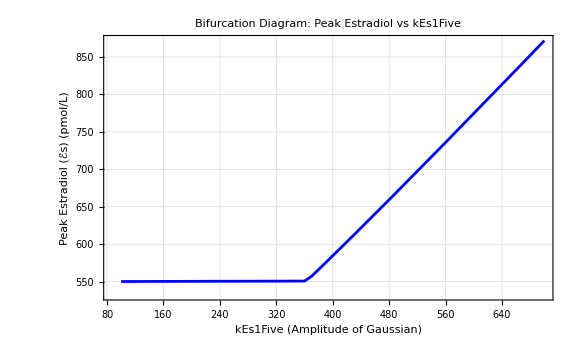

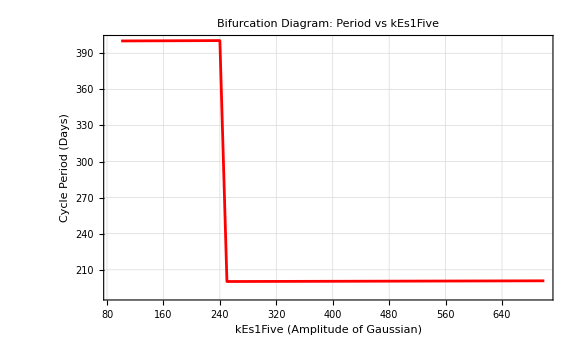

```mathematica
(*Estradiol model (Fifth iteration) with varying kEs1Five*)EsFive[t_,kEs1Five_]:=Es0Five+AEs1Five Sin[(2 Pi/28) (t-phiEs1Five)]+kEs1Five Exp[-((t-tLHFive)^2)/(2 sigmaLHFive^2)]+kEs2Five Exp[-((t-tSmoothFive)^2)/(2 sigmaSmoothFive^2)];

(*Define parameters for the estradiol model*)
Es0Five=150;AEs1Five=300;phiEs1Five=14;
kEs2Five=100;tLHFive=14;sigmaLHFive=2;
tSmoothFive=21;sigmaSmoothFive=3;

(*Function to find peak estradiol levels as the metric*)
findPeakEstradiol[kEs1Five_]:=Max[Table[EsFive[t,kEs1Five],{t,0,28,0.1}]];

(*Function to compute period of estradiol oscillations*)
findPeriodEstradiol[kEs1Five_]:=Module[{peaks,tValues},peaks=FindPeaks[Table[EsFive[t,kEs1Five],{t,0,28,0.1}]];
tValues=peaks[[All,2]];
If[Length[tValues]>1,Mean[Differences[tValues]],0]];

(*Parameter range for kEs1Five*)
parameterRange=Table[k,{k,100,700,10}];

(*Compute peak estradiol values for each parameter*)
bifurcationDataPeaks=Table[{k,findPeakEstradiol[k]},{k,parameterRange}];

(*Compute period values for each parameter*)
bifurcationDataPeriods=Table[{k,findPeriodEstradiol[k]},{k,parameterRange}];

(*Plot the bifurcation diagram:Peak estradiol*)
bifurcationDiagramPeaks=ListPlot[bifurcationDataPeaks,Joined->True,PlotStyle->Blue,PlotRange->All,PlotLabel->"Bifurcation Diagram: Peak Estradiol vs kEs1Five",Frame->True,FrameLabel->{"kEs1Five (Amplitude of Gaussian)","Peak Estradiol (ℰs) (pmol/L)"},GridLines->Automatic,ImageSize->Large];

(*Plot the bifurcation diagram:Cycle period*)
bifurcationDiagramPeriods=ListPlot[bifurcationDataPeriods,Joined->True,PlotStyle->Red,PlotRange->All,PlotLabel->"Bifurcation Diagram: Period vs kEs1Five",Frame->True,FrameLabel->{"kEs1Five (Amplitude of Gaussian)","Cycle Period (Days)"},GridLines->Automatic,ImageSize->Large];

(*Display the bifurcation diagrams*)
bifurcationDiagramPeaks
bifurcationDiagramPeriods
```

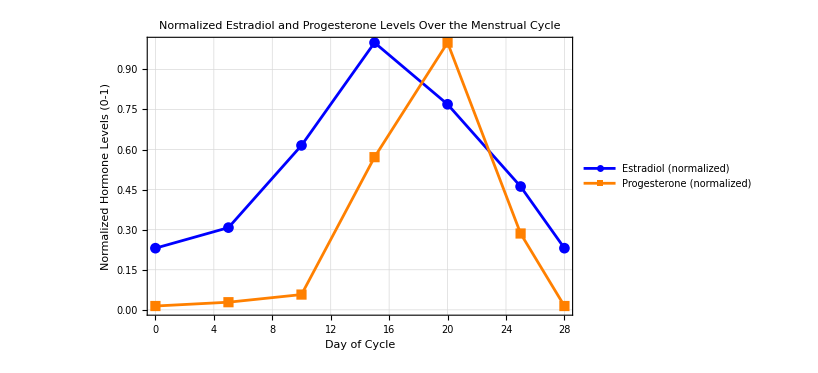

```mathematica
(*Provided hormone data for estradiol and progesterone*)estradiolHormoneData={{0,150},{5,200},{10,400},{15,650},{20,500},{25,300},{28,150}};
progesteroneHormoneData={{0,0.5},{5,1},{10,2},{15,20},{20,35},{25,10},{28,0.5}};

(*Interpolating the data for continuous hormone functions*)
estradiolFunction[t_]:=Interpolation[estradiolHormoneData][t];
progesteroneFunction[t_]:=Interpolation[progesteroneHormoneData][t];

(*Define dynamic energy level function based on hormone levels*)
dynamicEnergyLevelFunction[t_,estradiolFactor_,progesteroneFactor_,interactionFactor_]:=estradiolFactor*estradiolFunction[t]-progesteroneFactor*progesteroneFunction[t]+interactionFactor*estradiolFunction[t]*progesteroneFunction[t];

(*Normalize energy levels to a 0-1 range dynamically*)
normalizedDynamicEnergyLevelFunction[t_,estradiolFactor_,progesteroneFactor_,interactionFactor_]:=Module[{energyRange,energyLevel},energyLevel=Table[dynamicEnergyLevelFunction[t,estradiolFactor,progesteroneFactor,interactionFactor],{t,0,28,0.1}];
energyRange={Min[energyLevel],Max[energyLevel]};
Rescale[dynamicEnergyLevelFunction[t,estradiolFactor,progesteroneFactor,interactionFactor],energyRange,{0,1}]];

(*Interactive plot with sliders*)
Manipulate[Plot[normalizedDynamicEnergyLevelFunction[t,estradiolFactor,progesteroneFactor,interactionFactor],{t,0,28},PlotRange->{0,1},PlotLabel->"Normalized Energy Levels Based on Dynamic Hormone Contributions",Frame->True,FrameLabel->{"Day of Cycle","Normalized Energy Level (0-1)"},GridLines->Automatic,ImageSize->Large],{{estradiolFactor,0.8},0,1,0.1,Appearance->"Labeled"},{{progesteroneFactor,0.5},0,1,0.1,Appearance->"Labeled"},{{interactionFactor,0.1},0,0.5,0.05,Appearance->"Labeled"}]
```

```mathematica
(*Provided hormone data for estradiol and progesterone*)estradiolHormoneData={{0,150},{5,200},{10,400},{15,650},{20,500},{25,300},{28,150}};
progesteroneHormoneData={{0,0.5},{5,1},{10,2},{15,20},{20,35},{25,10},{28,0.5}};

(*Interpolating the data for continuous hormone functions*)
estradiolFunction[t_]:=Interpolation[estradiolHormoneData][t];
progesteroneFunction[t_]:=Interpolation[progesteroneHormoneData][t];

(*Define energy level function based on hormone levels*)
estradiolContributionFactor=0.8; (*Positive contribution of estradiol to energy*)
progesteroneDampeningFactor=0.5; (*Negative contribution of progesterone to energy*)
hormoneInteractionFactor=0.1;  (*Interaction coefficient between estradiol and progesterone*)

energyLevelFunction[t_]:=estradiolContributionFactor*estradiolFunction[t]-progesteroneDampeningFactor*progesteroneFunction[t]+hormoneInteractionFactor*estradiolFunction[t]*progesteroneFunction[t];

(*Normalize energy levels to a 0-1 range*)
energyLevelRange={Min[Table[energyLevelFunction[t],{t,0,28,0.1}]],Max[Table[energyLevelFunction[t],{t,0,28,0.1}]]};
normalizedEnergyLevelFunction[t_]:=Rescale[energyLevelFunction[t],energyLevelRange,{0,1}];

(*Plot normalized energy levels based on known hormone levels*)
Plot[normalizedEnergyLevelFunction[t],{t,0,28},PlotRange->{0,1},PlotLabel->"Normalized Energy Levels Based on Known Hormone Data",Frame->True,FrameLabel->{"Day of Cycle","Normalized Energy Level (0-1)"},GridLines->Automatic,ImageSize->Large]
```

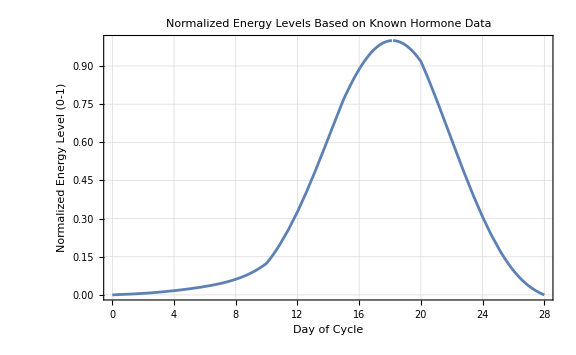

```mathematica
(*Precompute energy range for normalization*)precomputedEnergyRange[estradiolFactor_,progesteroneFactor_,interactionFactor_]:=Module[{energyValues},energyValues=Table[dynamicEnergyLevelFunction[t,estradiolFactor,progesteroneFactor,interactionFactor],{t,0,28,0.1}];
{Min[energyValues],Max[energyValues]}];
```

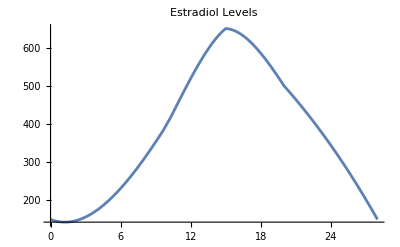

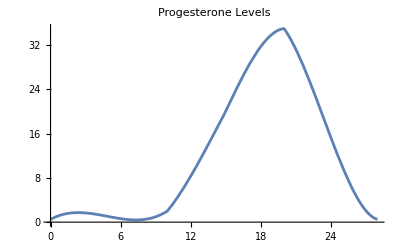

```mathematica
(*Provided hormone data for estradiol and progesterone*)estradiolHormoneData={{0,150},{5,200},{10,400},{15,650},{20,500},{25,300},{28,150}};
progesteroneHormoneData={{0,0.5},{5,1},{10,2},{15,20},{20,35},{25,10},{28,0.5}};

(*Interpolating the data for continuous hormone functions*)
estradiolFunction[t_]:=Interpolation[estradiolHormoneData][t];
progesteroneFunction[t_]:=Interpolation[progesteroneHormoneData][t];

(*Define dynamic energy level function based on hormone levels*)
dynamicEnergyLevelFunction[t_,estradiolFactor_,progesteroneFactor_,interactionFactor_]:=estradiolFactor*estradiolFunction[t]-progesteroneFactor*progesteroneFunction[t]+interactionFactor*estradiolFunction[t]*progesteroneFunction[t];
(*Normalize energy levels dynamically using precomputed range*)normalizedDynamicEnergyLevelFunction[t_,estradiolFactor_,progesteroneFactor_,interactionFactor_]:=Module[{range},range=precomputedEnergyRange[estradiolFactor,progesteroneFactor,interactionFactor];
Rescale[dynamicEnergyLevelFunction[t,estradiolFactor,progesteroneFactor,interactionFactor],range,{0,1}]];

(*Interactive plot with sliders*)
Manipulate[Plot[normalizedDynamicEnergyLevelFunction[t,estradiolFactor,progesteroneFactor,interactionFactor],{t,0,28},PlotRange->{0,1},PlotLabel->"Normalized Energy Levels Based on Dynamic Hormone Contributions",Frame->True,FrameLabel->{"Day of Cycle","Normalized Energy Level (0-1)"},GridLines->Automatic,ImageSize->Large],{{estradiolFactor,0.8},0,1,0.1,Appearance->"Labeled"},{{progesteroneFactor,0.5},0,1,0.1,Appearance->"Labeled"},{{interactionFactor,0.1},0,0.5,0.05,Appearance->"Labeled"}]
(*Test estradiol and progesterone functions*)Plot[estradiolFunction[t],{t,0,28},PlotLabel->"Estradiol Levels"]
Plot[progesteroneFunction[t],{t,0,28},PlotLabel->"Progesterone Levels"]
```

## Other experiments: Constructing a typical cycle

SetDelayed::write: Tag Integer in 28[t_] is Protected.

$Failed

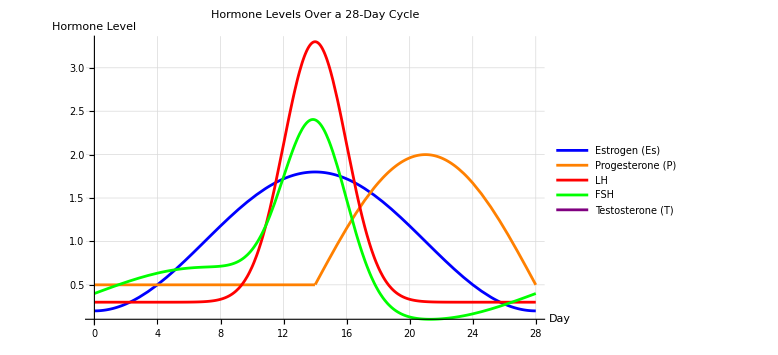

```mathematica
(*Base hormone functions for a 28-day cycle*)
Es[t_] := 1 + 0.8 Sin[(2 Pi/28) t - Pi/2] (*Estrogen*)
P[t_] := Piecewise[{{0.5 + 1.5 Sin[(2 Pi/28) (t - 14)], t >= 14}}, 0.5] (*Progesterone*)
LH[t_] := 0.3 + 3 Exp[-(t - 14)^2/8] (*Luteinizing Hormone*)
FSH[t_] := 0.4 + 0.3 Sin[(2 Pi/28) t] + 2 Exp[-(t - 14)^2/8] (*Follicle-Stimulating Hormone*)
T[t_] := 0.8 + 0.2 Sin[(2 Pi/28) t - Pi] (*Testosterone*)

(*Plot the hormone functions*)Plot[{Es[t],P[t],LH[t],FSH[t],T[t]},{t,0,28},PlotLegends->{"Estrogen (Es)","Progesterone (P)","LH","FSH","Testosterone (T)"},PlotStyle->{Blue,Orange,Red,Green,Purple},AxesLabel->{"Day","Hormone Level"},PlotRange->All,GridLines->Automatic,ImageSize->Large,PlotLabel->"Hormone Levels Over a 28-Day Cycle"]
```

### Cortisol impacts on the hormones

```mathematica
(*Base hormone functions for a 28-day cycle*)
Es[t_]:=1+0.8 Sin[(2 Pi/28) t-Pi/2] (*Estrogen*)
P[t_]:=Piecewise[{{0.5+1.5 Sin[(2 Pi/28) (t-14)],t>=14}},0.5] (*Progesterone*)
LH[t_]:=0.3+3 Exp[-(t-14)^2/8] (*Luteinizing Hormone*)
FSH[t_]:=0.4+0.3 Sin[(2 Pi/28) t]+2 Exp[-(t-14)^2/8] (*Follicle-Stimulating Hormone*)
T[t_]:=0.8+0.2 Sin[(2 Pi/28) t-Pi] (*Testosterone*)

(*Cortisol-modified hormone functions for each phase*)
ModifiedE[t_,cortisol_]:=Es[t]-cortisol[Phase[t]]*0.1 (*Cortisol suppresses estrogen*)
ModifiedP[t_,cortisol_]:=P[t]+cortisol[Phase[t]]*0.05 (*Cortisol increases progesterone*)
ModifiedLH[t_,cortisol_]:=LH[t]-cortisol[Phase[t]]*0.15 (*Cortisol suppresses LH*)
ModifiedFSH[t_,cortisol_]:=FSH[t]-cortisol[Phase[t]]*0.1 (*Cortisol suppresses FSH*)
ModifiedT[t_,cortisol_]:=T[t]+cortisol[Phase[t]]*0.05 (*Cortisol mildly boosts testosterone*)

(*Define the menstrual cycle phases*)
Phase[t_]:=Piecewise[{{"Menstrual",0<=t<5},{"Follicular",5<=t<13},{"Ovulatory",13<=t<16},{"Luteal",16<=t<=28}}]

(*Interactive manipulation to adjust cortisol for each phase*)
Manipulate[Module[{cortisolFunction},cortisolFunction=<|"Menstrual"->menstrualCort,"Follicular"->follicularCort,"Ovulatory"->ovulatoryCort,"Luteal"->lutealCort|>;
Plot[{ModifiedEs[t,cortisolFunction],
ModifiedP[t,cortisolFunction],
ModifiedLH[t,cortisolFunction],
ModifiedFSH[t,cortisolFunction],ModifiedT[t,cortisolFunction]},{t,0,28},PlotLegends->{"Estrogen (Es)","Progesterone (P)","LH","FSH","Testosterone (T)"},PlotStyle->{Blue,Orange,Red,Green,Purple},PlotRange->{{0,28},{0,4}},AxesLabel->{"Day","Hormone Level"},GridLines->{Range[0,28,7],None},Epilog->{Text["Menstrual",{2.5,3.8},Background->White],Text["Follicular",{9,3.8},Background->White],Text["Ovulatory",{14.5,3.8},Background->White],Text["Luteal",{22,3.8},Background->White]},ImageSize->Large,PlotLabel->"Hormone Levels with Phase-Based Cortisol Adjustments"]],{{menstrualCort,0,"Menstrual Cortisol"},0,3,0.1,Appearance->"Labeled"},{{follicularCort,0,"Follicular Cortisol"},0,3,0.1,Appearance->"Labeled"},{{ovulatoryCort,0,"Ovulatory Cortisol"},0,3,0.1,Appearance->"Labeled"},{{lutealCort,0,"Luteal Cortisol"},0,3,0.1,Appearance->"Labeled"}]
```

SetDelayed::write: Tag Integer in 28[t_] is Protected.

$Failed